# Math 223: Homework 7

Ali Heydari

March. 18th, 2021

## Problem 1

Find the first two terms of the asymptotic expansion of:

For this Laplace integral (which is of the form ), we can perform IBP to obtain the asymptotic expansion. Doing IBP, will get:
 = 

Now if we continue with IBP, then the next term will be . So we will show that  is smaller than the first two terms, so that we can get an asymptotic relation that approximates  well.

```mathematica
numerator = (1/x) *  Integrate[E^(-x*t)/t^2,{t,5,9},Assumptions->x>0]
```

((1/45 ⅇ^(-9 x) (-5+9 ⅇ^(4 x))-x ExpIntegralEi[-9 x]+x ExpIntegralEi[-5 x]) (Assumptions→x>0))/x

```mathematica
denom = -E^(-9x)/(9x) +E^(-5x)/(5x)
```

-ⅇ^(-9 x)/(9 x)+ⅇ^(-5 x)/(5 x)

```mathematica
Limit[numerator/denom, x-> ∞]
```

0

this result solidifies that the remainder terms in the asymptotic expansion will be smaller than the first two terms we recovered, meaning



 So now we can see how well our approximations have been using a LogPlot:

```mathematica
exactSol=Integrate[E^(-x*t)/t,{t,5,9}]
```

ExpIntegralEi[-9 x]-ExpIntegralEi[-5 x]

```mathematica
approx = denom
```

-ⅇ^(-9 x)/(9 x)+ⅇ^(-5 x)/(5 x)

Now plotting the semi-log plot and the error plot

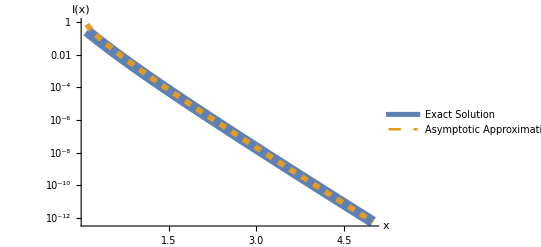

```mathematica
LogPlot[{exactSol,approx},{x,0.1,5},PlotStyle->{Directive[Solid,Thickness[0.02]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact Solution", "Asymptotic Approximation"}]
```

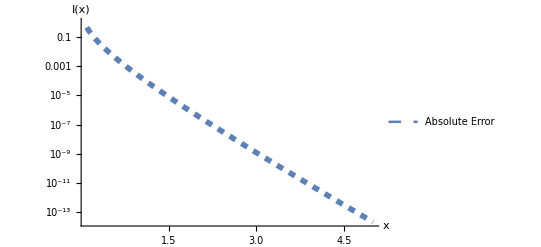

```mathematica
absErr = Abs[exactSol - approx];
LogPlot[absErr ,{x,0.1,5},PlotStyle->{Directive[Solid,Thickness[0.02]],Directive[Dashed,Thickness[0.01]]}, AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Absolute Error"}]
```

these plots show that for x being close to 0, our approximation is not so well, but if we move slightly pass 1, our error becomes very small! (this is very impressive, since we approximated the leading behavior as x → ∞!!)

## Problem 2

Use Watson’s lemma to determine the asymptotic expansion of:

At this point, our first bet should be to start with integration by parts to obtain an asymptotic expansion; however, we are told to use Watson’s lemma and IBP fails for this case. The next thing we want to try is to see if the integral satisfies the conditions of Watson’s lemma. That is:

(i) if  is real and continuous:  this is true since 

(ii)  attains its maximum on the given interval : true: at  = c, since  is monotonically decreasing

(iii) Does  with   and ? Yes, since , with -1/3 > -1 and

then since we satisfy these assumptions, we can say that only the immediate neighborhood of  contributes to the full asymptotic expansion of  for large  . So this means that for some value , we have the following:

Now to explicitly find the the asymptotic expansion, we can use the Taylor series of  about t= c = 0, which is  . So now we can rewrite our integral to be:

using the results of Watson’s lemma with bounding this integral by a positive constant, and the fact that most “mass” is around the point c and anything outside of this neighborhood will be negligible, we can let the bound go to infinity. Also since the series converges uniformly, we can reverse the integration order:

Now doing a substitution with u = xt  we can obtain the following integral

which looks like gamma function exactly. So now we arrive at the conclusion of Watson’s lemma where we have:

Now to see how well we have approximated this value, we will plot the asymptotic solution against the exact one:

```mathematica
ExactIntegral[x_] = Integrate[ⅇ^(-x t)/t^(1/3)*Cos[t],{t,0,Pi},Assumptions->x>0]
```

1/2 (-π^(2/3) (ExpIntegralE[1/3,π (-ⅈ+x)]+ExpIntegralE[1/3,π (ⅈ+x)])+(1/(-ⅈ+x)^(2/3)+1/(ⅈ+x)^(2/3)) Gamma[2/3])

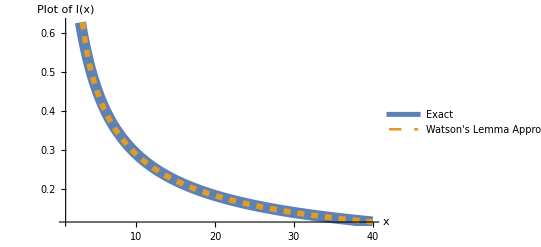

```mathematica
approxSol = Sum[(-1)^n Gamma[(-1/3) +2n + 1]/x^((-1/3)+ 2n+1),{n,0,2}];
Plot[{ExactIntegral[x],approxSol },{x,1,40},
PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Plot of I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact","Watson's Lemma Approximation"}]
```

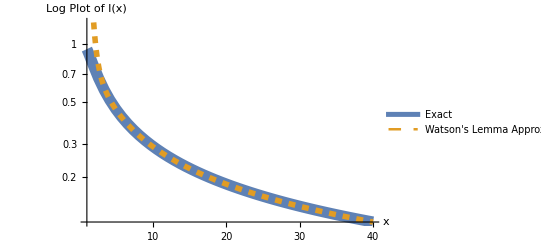

```mathematica
LogPlot[{ExactIntegral[x],approxSol },{x,1,40},
PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Log Plot of I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact","Watson's Lemma Approximation"}]
```

both of our plots show a very good approximation of the behavior of the integral for values after 4 (since, you know, 4 is infinity). This is expected since we approximated the integral as x→ ∞. This is a great example of showing the power of Watson’s lemma, when ϕ(t) is monotonic.

## Problem 3

Use Laplace’s method to determine the leading behavior of:

To see how if we can use Laplace’s method for this integral, we can check:

(i) is  monotonic on [-1/2,1/2]? No, which is good because this is what Laplace’s method is for!

(ii) Is there a point c ∈  (-1/2,1/2) such that  ? yes, at least the 4th order derivative at 0 will not be zero. As shown below:

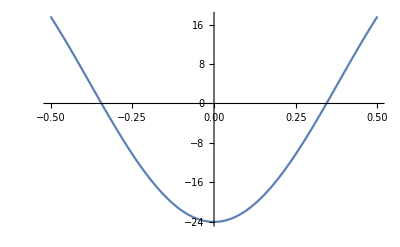

```mathematica
Plot[Evaluate[D[-Sin[x]^4,{x,4}]],{x,-1/2,1/2}]
```

Now that we have established that using Laplace’s method is appropriate, we can do a Taylor expansion of  about 0, that is we can simply replace this term with

```mathematica
Series[Sin[t]^4,{t,0,10}]
```

t^4-(2 t^6)/3+t^8/5-(34 t^10)/945+O[t]^11

which we will take to be t^4. So now we can rewrite the integral as

Now we can do a substitution for dt and obtain:

Now if we take a close look at this, we see that almost have a Gamma function, but instead of going from 0 to ∞ we have the bounds -∞ to ∞. using the definition in the book (pp. 267), this means that we will have: 



Now that we have computed this asymptotic approximation, we can see how well this works compared to the exact solution.

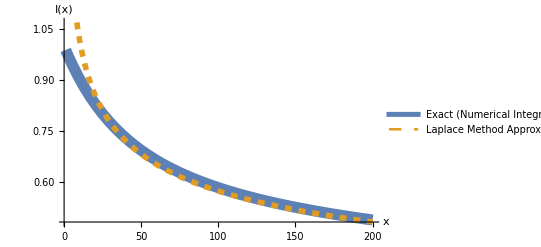

```mathematica
Plot[{NIntegrate[Exp[-x*(Sin[t])^4],{t,-1/2,1/2}],Gamma[1/4]/(2*x^(1/4))},{x,1,200},PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact (Numerical Integral)","Laplace Method Approximation"}]
```

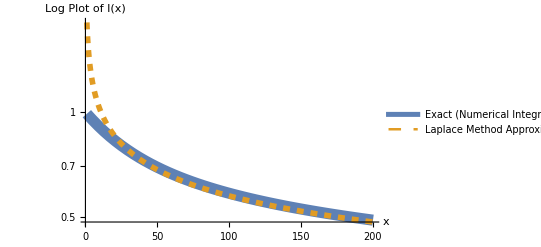

```mathematica
LogPlot[{NIntegrate[Exp[-x*(Sin[t])^4],{t,-1/2,1/2}],Gamma[1/4]/(2*x^(1/4))},{x,1,200},PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["Log Plot of I(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact (Numerical Integral)","Laplace Method Approximation"}]
```

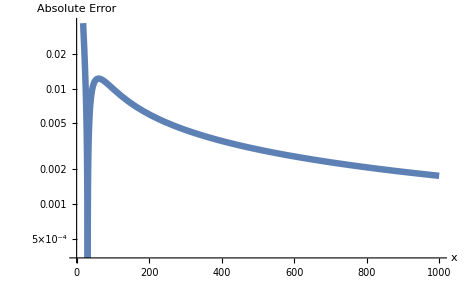

```mathematica
LogPlot[Abs[NIntegrate[Exp[-x*(Sin[t])^4],{t,-1/2,1/2}]-Gamma[1/4]/(2*x^(1/4))],{x,1,1000},
PlotStyle-> Directive[Solid,Thickness[0.01]],AxesLabel->{Style["x",Italic,18],Style["Absolute Error", Italic, 18]}, TicksStyle->Directive[FontSize->14]]
```

as we can see, our approximation gets better as x increases, with large error values for x bring close to 0; this makes sense since we are approximating the asymptotic behavior as . I do think better approximation is possible if we keep going with more terms in the Taylor expansion that we used to perform the integration with, or a different method.